```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]]
```

/Users/ethanspangler/StabilityProject

Plots of Freedonia, Merika, and Kleptopia for low initial dissent.

```mathematica
Freedonia =Import["dataFreedonia.mx"] // Dataset;
Merika =Import["dataMerika.mx"] // Dataset;
Kleptopia=Import["dataKleptopia.mx"]//Dataset;
Cathay=Import["dataCathay.mx"]//Dataset;
Rentistan=Import["dataRentistan.mx"]//Dataset;
Develpolus=Import["dataDevelpolus.mx"]//Dataset;
Bellicostia=Import["dataBellicostia.mx"]//Dataset;
Hippieberg=Import["dataHippieberg.mx"]//Dataset;
```

New lines to convert Scientific form to plotable form:

```mathematica
Freedonia = Freedonia/.ScientificForm[n_,rest___]->n
Merika = Merika/.ScientificForm[n_,rest___]->n
Kleptopia = Kleptopia/.ScientificForm[n_,rest___]->n
Cathay= Cathay/.ScientificForm[n_,rest___]->n
Rentistan= Rentistan/.ScientificForm[n_,rest___]->n
Develpolus= Develpolus/.ScientificForm[n_,rest___]->n
Bellicostia= Bellicostia/.ScientificForm[n_,rest___]->n
Hippieberg= Hippieberg/.ScientificForm[n_,rest___]->n
```

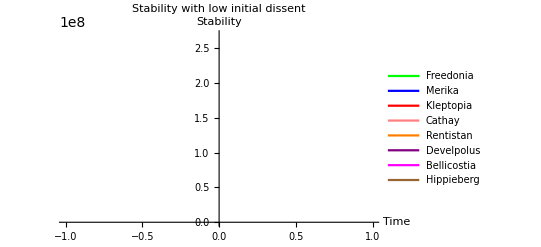

```mathematica
ListLinePlot[{Freedonia[All,{1,3}]//Normal,Merika[All,{1,3}]//Normal,Kleptopia[All,{1,3}] //Normal ,
Cathay[All,{1,3}],
Rentistan[All,{1,3}],
Develpolus[All,{1,3}],
Bellicostia[All,{1,3}],
Hippieberg[All,{1,3}]},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with low initial dissent", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```

Initial plotting of the Shocks, with the shock affecting government resrouces, R, in period 100, reducing R to 75% previous values.

```mathematica
FreedoniaRSHOCK =Import["dataFreedoniaRSHOCK.mx"] // Dataset;
MerikaRSHOCK  =Import["dataMerikaRSHOCK.mx"] // Dataset;
KleptopiaRSHOCK =Import["dataKleptopiaRSHOCK.mx"]//Dataset;
CathayRSHOCK =Import["dataCathayRSHOCK.mx"]//Dataset;
RentistanRSHOCK =Import["dataRentistanRSHOCK.mx"]//Dataset;
DevelpolusRSHOCK =Import["dataDevelpolusRSHOCK.mx"]//Dataset;
BellicostiaRSHOCK =Import["dataBellicostiaRSHOCK.mx"]//Dataset;
HippiebergRSHOCK =Import["dataHippiebergRSHOCK.mx"]//Dataset;
```

```mathematica
FreedoniaRSHOCK  = FreedoniaRSHOCK /.ScientificForm[n_,rest___]->n
MerikaRSHOCK  = MerikaRSHOCK /.ScientificForm[n_,rest___]->n
KleptopiaRSHOCK  = KleptopiaRSHOCK /.ScientificForm[n_,rest___]->n
CathayRSHOCK = CathayRSHOCK /.ScientificForm[n_,rest___]->n
RentistanRSHOCK = RentistanRSHOCK /.ScientificForm[n_,rest___]->n
DevelpolusRSHOCK = DevelpolusRSHOCK /.ScientificForm[n_,rest___]->n
BellicostiaRSHOCK= BellicostiaRSHOCK /.ScientificForm[n_,rest___]->n
HippiebergRSHOCK = HippiebergRSHOCK /.ScientificForm[n_,rest___]->n
```

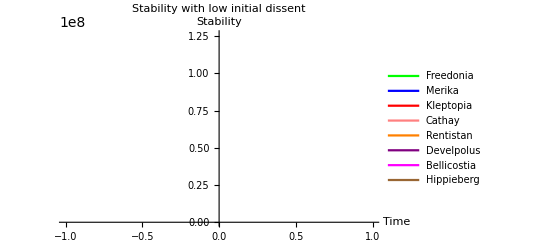

```mathematica
ListLinePlot[{FreedoniaRSHOCK[All,{1,3}]//Normal,MerikaRSHOCK[All,{1,3}]//Normal,KleptopiaRSHOCK[All,{1,3}] //Normal ,
CathayRSHOCK[All,{1,3}],
RentistanRSHOCK[All,{1,3}],
DevelpolusRSHOCK[All,{1,3}],
BellicostiaRSHOCK[All,{1,3}],
HippiebergRSHOCK[All,{1,3}]},PlotLegends->{"Freedonia","Merika","Kleptopia","Cathay","Rentistan","Develpolus","Bellicostia","Hippieberg"},PlotStyle->{Green,Blue,Red,Pink,Orange,Purple,Magenta,Brown},
PlotLabel->Style["Stability with R shock at period 100", FontSize->12],
PlotRange->Full,AxesLabel->{"Time","Stability"}]
```